# Modelo Bose - Hubbard en la Aproximación de Campo Medio

## Novoa Gastaldi Alejandro Silvestre

(silvestre.novoa@ciencias.unam.mx)

## 03/2019

```mathematica
Clear["Global`*"]
```

#### Hamiltoniano de Bose-Hubbard con μ/U =0.5 para una base de 4 elementos.

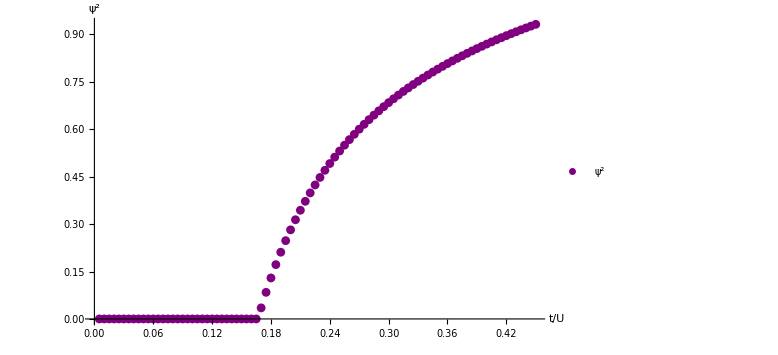

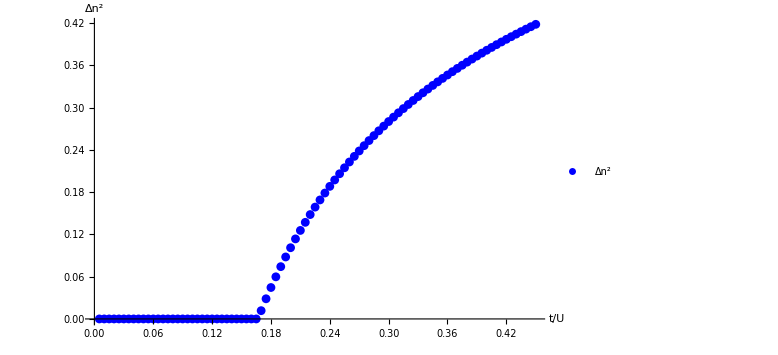

```mathematica
Clear["Global`*"]



nDimensiones=4.;

(*Parametros Iniciales*)
U=1.;
Z=1.;

ψ00=0.1;
t0=0.005;
μ0=0.5;

(*Error de iteración*)
ErrorMax=0.00001;
NPuntos=90.;

(*Parametros Variables*)
ψ=Table[ψ00,{i,1,NPuntos}];
t=Table[t0*i,{i,1,NPuntos}];
μ=Table[μ0*i,{i,1,NPuntos}];
ψ0=Table[ψ00,{i,1,NPuntos}];
Dn2=Table[0,{i,1,NPuntos}];



(*Funciones para la construcción del Hamiltoniano*)
FDiagonal[i_,ψ_,t_,U_,μ_,Z_]:=Module[{i0=i,ψ0=ψ,t0=t,U0=U,μ0=μ,Z0=Z},U0*(i0-1.)*i0/2.-μ0*i0+1.*Z0*t0*ψ0^2];
FNoDiagonal[i_,ψ_,t_,Z_]:=Module[{i0=i,ψ0=ψ,t0=t,Z0=Z},1.*Z0*t0*ψ0*Sqrt[i0] ];


(*Lo siguiente se realiza en un do que varia el parametro t*)
(*Se contruye el Hamiltoniano para el primer caso con ψinicial. Se calcula el estado base. Se calcula respecto al edoBase ψ0=<b>, con b el operador de aniquilación. Se puede estimar un error como   Abs[ ψ0-ψ ] tal que si es mayor al ErrorMax, se define ψ=ψ0 y se itera lo anterior en un While  *)
(*Una vez que termine cada iteración del while, con el ultimo estado base calculado, se estima el parametro de fluctuación de particulas <n^2>-<n>^2 *)
Do[    {
H=Table[Table[0,{i,1,nDimensiones}],{j,1,nDimensiones}];
Do[H[[i,i+1]]=FNoDiagonal[ i,ψ[[ln]],t[[ln]],Z ],{i,1,nDimensiones-1,1}];
H=H+ConjugateTranspose[H];
Do[H[[i,i]]=-FDiagonal[ i-1,ψ[[ln]],t[[ln]],U,μ[[1]],Z ],{i,1,nDimensiones,1}];

EdoBase=Flatten[ Eigensystem[H,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[2]] ];

ψ0[[ln]]=Sum[Sqrt[i]*EdoBase[[i]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}];

While[          Abs[ ψ0[[ln]]-ψ[[ln]] ]>ErrorMax,
ψ[[ln]]=ψ0[[ln]];
 
H=Table[Table[0,{i,1,nDimensiones}],{j,1,nDimensiones}];
Do[H[[i,i+1]]=FNoDiagonal[ i,ψ[[ln]],t[[ln]],Z ],{i,1,nDimensiones-1,1}];
H=H+ConjugateTranspose[H];
Do[H[[i,i]]=-FDiagonal[ i-1,ψ[[ln]],t[[ln]],U,μ[[1]],Z ],{i,1,nDimensiones,1}];

EdoBase=Flatten[ Eigensystem[H,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[2]] ];

ψ0[[ln]]=Sum[Sqrt[i]*EdoBase[[i]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}]          ], 
Dn2[[ln]]=Sum[i^2*EdoBase[[i+1]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}]-Sum[i*EdoBase[[i+1]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}]^2           } ,
                                     {ln,1,NPuntos,1}]


(*Se contruyen los conjuntos de puntos (t,ψ^2) y (t,Dn2) que se graficaran *)
ψ2=Table[{t[[i]],(ψ0[[i]])^2},{i,1,NPuntos}];
DnCuadrado=Table[{t[[i]],Dn2[[i]]},{i,1,NPuntos}];


ListPlot[ψ2,ImageSize->Large,AxesStyle->{Black,Black},PlotStyle->{Thick,Purple},PlotLegends->{"ψ^2"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"t/U" ,"ψ^2"}]
ListPlot[DnCuadrado,ImageSize->Large,AxesStyle->{Black,Black},PlotStyle->{Thick,Blue},PlotLegends->{"Δn^2"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"t/U" ,"Δn^2"}]
```

#### Hamiltoniano de Bose-Hubbard en función de t y μ para una base de 4 elementos.

-Graphics3D-

-Graphics3D-

Diagrama de Fase

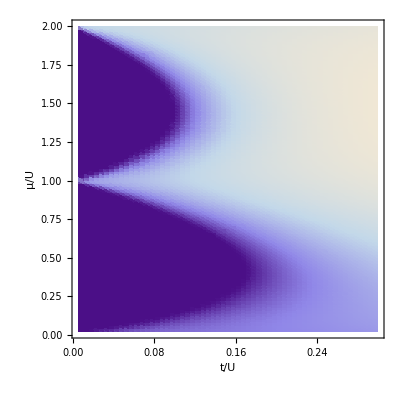

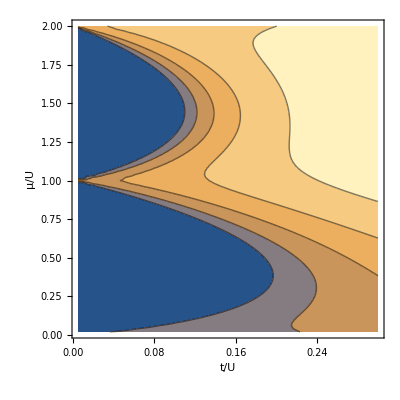

```mathematica
Clear["Global`*"]



nDimensiones=4.;

(*Parametros Iniciales*)
U=1.;
Z=1.;

ψ00=0.1;
t0=0.005;
μ0=0.02;

(*Error de iteración*)
ErrorMax=0.00001;
tNPuntos=60.;
μNPuntos=100.;

(*Parametros Variables*)
ψ=Table[Table[ψ00,{i,1,μNPuntos}],{j,1,tNPuntos}];
t=Table[t0*i,{i,1,tNPuntos}];
μ=Table[μ0*i,{i,1,μNPuntos}];
ψ0=Table[Table[ψ00,{i,1,μNPuntos}],{j,1,tNPuntos}];
Dn2=Table[Table[0,{i,1,μNPuntos}],{j,1,tNPuntos}];



(*Funciones para la construcción del Hamiltoniano*)
FDiagonal[i_,ψ_,t_,U_,μ_,Z_]:=Module[{i0=i,ψ0=ψ,t0=t,U0=U,μ0=μ,Z0=Z},U0*(i0-1.)*i0/2.-μ0*i0+1.*Z0*t0*ψ0^2];
FNoDiagonal[i_,ψ_,t_,Z_]:=Module[{i0=i,ψ0=ψ,t0=t,Z0=Z},1.*Z0*t0*ψ0*Sqrt[i0] ];


(* Se extiende el Do para las variaciones de μ *)
Do[
(*Lo siguiente se realiza en un do que varia el parametro t*)
(*Se contruye el Hamiltoniano para el primer caso con ψinicial. Se calcula el estado base. Se calcula respecto al edoBase ψ0=<b>, con b el operador de aniquilación. Se puede estimar un error como   Abs[ ψ0-ψ ] tal que si es mayor al ErrorMax, se define ψ=ψ0 y se itera lo anterior en un While  *)
(*Una vez que termine cada iteración del while, con el ultimo estado base calculado, se estima el parametro de fluctuación de particulas <n^2>-<n>^2 *)
Do[    {
H=Table[Table[0,{i,1,nDimensiones}],{j,1,nDimensiones}];
Do[H[[i,i+1]]=FNoDiagonal[ i,ψ[[ln,kn]],t[[ln]],Z ],{i,1,nDimensiones-1,1}];
H=H+ConjugateTranspose[H];
Do[H[[i,i]]=-FDiagonal[ i-1,ψ[[ln,kn]],t[[ln]],U,μ[[kn]],Z ],{i,1,nDimensiones,1}];

EdoBase=Flatten[ Eigensystem[H,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[2]] ];

ψ0[[ln,kn]]=Sum[Sqrt[i]*EdoBase[[i]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}];

While[          Abs[ ψ0[[ln,kn]]-ψ[[ln,kn]] ]>ErrorMax,
ψ[[ln,kn]]=ψ0[[ln,kn]];
 
H=Table[Table[0,{i,1,nDimensiones}],{j,1,nDimensiones}];
Do[H[[i,i+1]]=FNoDiagonal[ i,ψ[[ln,kn]],t[[ln]],Z ],{i,1,nDimensiones-1,1}];
H=H+ConjugateTranspose[H];
Do[H[[i,i]]=-FDiagonal[ i-1,ψ[[ln,kn]],t[[ln]],U,μ[[kn]],Z ],{i,1,nDimensiones,1}];

EdoBase=Flatten[ Eigensystem[H,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[2]] ];

ψ0[[ln,kn]]=Sum[Sqrt[i]*EdoBase[[i]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}]          ], 
Dn2[[ln,kn]]=Sum[i^2*EdoBase[[i+1]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}]-Sum[i*EdoBase[[i+1]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}]^2           } ,
                                     {ln,1,tNPuntos,1}],
                                                             {kn,1,μNPuntos,1}]


(*Se contruyen los conjuntos de puntos (t,μ,ψ^2) y (t,μ,Dn2) que se graficaran *)
ψ2=Flatten[Table[Table[{t[[i]],μ[[kn]],(ψ0[[i,kn]])^2},{i,1,tNPuntos}],{kn,1,μNPuntos}],1];
DnCuadrado=Flatten[Table[Table[{t[[i]],μ[[kn]],Dn2[[i,kn]]},{i,1,tNPuntos}],{kn,1,μNPuntos}],1];


ListPointPlot3D[ψ2,PlotStyle->{Thick,Purple},PlotLegends->{"ψ^2"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"t/U" ,"μ/U","ψ^2"}]
ListPointPlot3D[DnCuadrado,PlotStyle->{Thick,Blue},PlotLegends->{"Δn^2"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"t/U" ,"μ/U","Δn^2"}]


(*Diagrama de Fase*)
Print[ Style["Diagrama de Fase",18,Bold,Blue]]
ListDensityPlot[ψ2,ColorFunction->"LakeColors",FrameLabel->{"t/U" ,"μ/U"},LabelStyle->{12.5,Black}]
ListContourPlot[ψ2,FrameLabel->{"t/U" ,"μ/U"},LabelStyle->{12.5,Black}]
```

#### Hamiltoniano de Bose-Hubbard en función de t y μ para una base de 5 elementos.

-Graphics3D-

-Graphics3D-

Diagrama de Fase

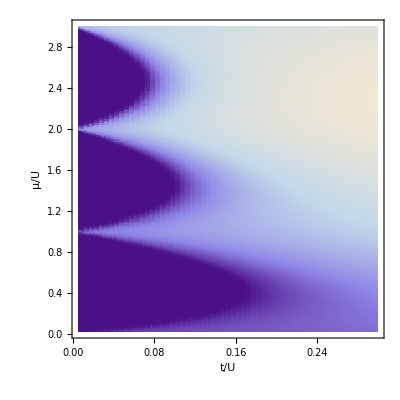

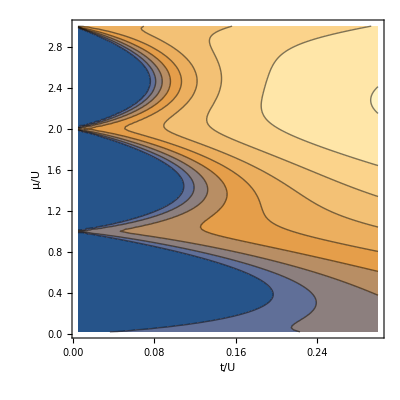

```mathematica
Clear["Global`*"]



nDimensiones=5.;

(*Parametros Iniciales*)
U=1.;
Z=1.;

ψ00=0.1;
t0=0.005;
μ0=0.02;

(*Error de iteración*)
ErrorMax=0.00001;
tNPuntos=60.;
μNPuntos=150.;

(*Parametros Variables*)
ψ=Table[Table[ψ00,{i,1,μNPuntos}],{j,1,tNPuntos}];
t=Table[t0*i,{i,1,tNPuntos}];
μ=Table[μ0*i,{i,1,μNPuntos}];
ψ0=Table[Table[ψ00,{i,1,μNPuntos}],{j,1,tNPuntos}];
Dn2=Table[Table[0,{i,1,μNPuntos}],{j,1,tNPuntos}];



(*Funciones para la construcción del Hamiltoniano*)
FDiagonal[i_,ψ_,t_,U_,μ_,Z_]:=Module[{i0=i,ψ0=ψ,t0=t,U0=U,μ0=μ,Z0=Z},U0*(i0-1.)*i0/2.-μ0*i0+1.*Z0*t0*ψ0^2];
FNoDiagonal[i_,ψ_,t_,Z_]:=Module[{i0=i,ψ0=ψ,t0=t,Z0=Z},1.*Z0*t0*ψ0*Sqrt[i0] ];


(* Se extiende el Do para las variaciones de μ *)
Do[
(*Lo siguiente se realiza en un do que varia el parametro t*)
(*Se contruye el Hamiltoniano para el primer caso con ψinicial. Se calcula el estado base. Se calcula respecto al edoBase ψ0=<b>, con b el operador de aniquilación. Se puede estimar un error como   Abs[ ψ0-ψ ] tal que si es mayor al ErrorMax, se define ψ=ψ0 y se itera lo anterior en un While  *)
(*Una vez que termine cada iteración del while, con el ultimo estado base calculado, se estima el parametro de fluctuación de particulas <n^2>-<n>^2 *)
Do[    {
H=Table[Table[0,{i,1,nDimensiones}],{j,1,nDimensiones}];
Do[H[[i,i+1]]=FNoDiagonal[ i,ψ[[ln,kn]],t[[ln]],Z ],{i,1,nDimensiones-1,1}];
H=H+ConjugateTranspose[H];
Do[H[[i,i]]=-FDiagonal[ i-1,ψ[[ln,kn]],t[[ln]],U,μ[[kn]],Z ],{i,1,nDimensiones,1}];

EdoBase=Flatten[ Eigensystem[H,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[2]] ];

ψ0[[ln,kn]]=Sum[Sqrt[i]*EdoBase[[i]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}];

While[          Abs[ ψ0[[ln,kn]]-ψ[[ln,kn]] ]>ErrorMax,
ψ[[ln,kn]]=ψ0[[ln,kn]];
 
H=Table[Table[0,{i,1,nDimensiones}],{j,1,nDimensiones}];
Do[H[[i,i+1]]=FNoDiagonal[ i,ψ[[ln,kn]],t[[ln]],Z ],{i,1,nDimensiones-1,1}];
H=H+ConjugateTranspose[H];
Do[H[[i,i]]=-FDiagonal[ i-1,ψ[[ln,kn]],t[[ln]],U,μ[[kn]],Z ],{i,1,nDimensiones,1}];

EdoBase=Flatten[ Eigensystem[H,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[2]] ];

ψ0[[ln,kn]]=Sum[Sqrt[i]*EdoBase[[i]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}]          ], 
Dn2[[ln,kn]]=Sum[i^2*EdoBase[[i+1]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}]-Sum[i*EdoBase[[i+1]]*Conjugate[EdoBase[[i+1]]],{i,1,nDimensiones-1,1}]^2           } ,
                                     {ln,1,tNPuntos,1}],
                                                             {kn,1,μNPuntos,1}]


(*Se contruyen los conjuntos de puntos (t,μ,ψ^2) y (t,μ,Dn2) que se graficaran *)
ψ2=Flatten[Table[Table[{t[[i]],μ[[kn]],(ψ0[[i,kn]])^2},{i,1,tNPuntos}],{kn,1,μNPuntos}],1];
DnCuadrado=Flatten[Table[Table[{t[[i]],μ[[kn]],Dn2[[i,kn]]},{i,1,tNPuntos}],{kn,1,μNPuntos}],1];


ListPointPlot3D[ψ2,PlotStyle->{Thick,Purple},PlotLegends->{"ψ^2"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"t/U" ,"μ/U","ψ^2"}]
ListPointPlot3D[DnCuadrado,PlotStyle->{Thick,Blue},PlotLegends->{"Δn^2"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"t/U" ,"μ/U","Δn^2"}]


(*Diagrama de Fase*)
Print[ Style["Diagrama de Fase",18,Bold,Blue]]
ListDensityPlot[ψ2,ColorFunction->"LakeColors",FrameLabel->{"t/U" ,"μ/U"},LabelStyle->{12.5,Black}]
ListContourPlot[ψ2,FrameLabel->{"t/U" ,"μ/U"},LabelStyle->{12.5,Black}]
```